```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Import[NotebookDirectory[]<>"../SMatrix/ResultsParser.wl"]
Directory[]
```

Global`Private`

C:\Users\marucha\Desktop\SMatrixBootstrap\pionScatteringResult

```mathematica
resultDirectories = FileNames["*_out"]
```

{cubic_coupling_n_12_j_24.max.gz_out,cubic_coupling_n_14_j_26.max.gz_out,cubic_coupling_n_16_j_28.max.gz_out,cubic_coupling_n_18_j_30.max.gz_out,cubic_coupling_n_4_j_16.max.gz_out,cubic_coupling_n_8_j_20.max.gz_out,quartic_coupling_imp_n_0_j_8.max.gz_out,quartic_coupling_imp_n_0_j_8.min.gz_out,quartic_coupling_imp_n_10_j_22.max.gz_out,quartic_coupling_imp_n_10_j_22.min.gz_out,quartic_coupling_imp_n_12_j_24.max.gz_out,quartic_coupling_imp_n_12_j_24.min.gz_out,quartic_coupling_imp_n_14_j_26.max.gz_out,quartic_coupling_imp_n_14_j_26.min.gz_out,quartic_coupling_imp_n_16_j_28.max.gz_out,quartic_coupling_imp_n_16_j_28.min.gz_out,quartic_coupling_imp_n_18_j_30.max.gz_out,quartic_coupling_imp_n_18_j_30.min.gz_out,quartic_coupling_imp_n_1_j_9.max.gz_out,quartic_coupling_imp_n_1_j_9.min.gz_out,quartic_coupling_imp_n_20_j_32.max.gz_out,quartic_coupling_imp_n_20_j_32.min.gz_out,quartic_coupling_imp_n_2_j_10.max.gz_out,quartic_coupling_imp_n_2_j_10.min.gz_out,quartic_coupling_imp_n_3_j_11.max.gz_out,quartic_coupling_imp_n_3_j_11.min.gz_out,quartic_coupling_imp_n_4_j_16.max.gz_out,quartic_coupling_imp_n_4_j_16.min.gz_out,quartic_coupling_imp_n_6_j_18.max.gz_out,quartic_coupling_imp_n_6_j_18.min.gz_out,quartic_coupling_imp_n_8_j_20.max.gz_out,quartic_coupling_imp_n_8_j_20.min.gz_out,quartic_coupling_n_10_j_20.max.gz_out,quartic_coupling_n_10_j_20.min.gz_out,quartic_coupling_n_10_j_22.max.gz_out,quartic_coupling_n_10_j_22.min.gz_out,quartic_coupling_n_12_j_24.max.gz_out,quartic_coupling_n_12_j_24.min.gz_out,quartic_coupling_n_14_j_26.max.gz_out,quartic_coupling_n_14_j_26.min.gz_out,quartic_coupling_n_16_j_28.max.gz_out,quartic_coupling_n_16_j_28.min.gz_out,quartic_coupling_n_18_j_30.max.gz_out,quartic_coupling_n_18_j_30.min.gz_out,quartic_coupling_n_8_j_20.max.gz_out,quartic_coupling_n_8_j_20.min.gz_out,quartic_coupling_with_pole_n_10_j_22.max.gz_out,quartic_coupling_with_pole_n_10_j_22.min.gz_out,quartic_coupling_with_pole_n_12_j_24.max.gz_out,quartic_coupling_with_pole_n_12_j_24.min.gz_out,quartic_coupling_with_pole_n_14_j_26.max.gz_out,quartic_coupling_with_pole_n_14_j_26.min.gz_out,quartic_coupling_with_pole_n_16_j_28.max.gz_out,quartic_coupling_with_pole_n_16_j_28.min.gz_out,quartic_coupling_with_pole_n_18_j_30.max.gz_out,quartic_coupling_with_pole_n_18_j_30.min.gz_out,quartic_coupling_with_pole_n_4_j_16.max.gz_out,quartic_coupling_with_pole_n_4_j_16.min.gz_out}

```mathematica
AFREE=1/(5760 π^2);
```

```mathematica
ParseFilename[name_]:=  StringCases[name,
"quartic_coupling_"~~variation:Longest[("imp_"|"with_pole_"|"")]~~"n_"~~n:NumberString~~"_j_"~~j:NumberString~~"."~~type:("max"|"min")~~".gz_out":><|"variation"->variation,"type"->type,"n"->ToExpression[n],"j"->ToExpression[j]|>]//First
```

```mathematica
ParseFilename/@resultDirectories
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

{First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],<|variation→imp_,type→max,n→0,j→8|>,<|variation→imp_,type→min,n→0,j→8|>,<|variation→imp_,type→max,n→10,j→22|>,<|variation→imp_,type→min,n→10,j→22|>,<|variation→imp_,type→max,n→12,j→24|>,<|variation→imp_,type→min,n→12,j→24|>,<|variation→imp_,type→max,n→14,j→26|>,<|variation→imp_,type→min,n→14,j→26|>,<|variation→imp_,type→max,n→16,j→28|>,<|variation→imp_,type→min,n→16,j→28|>,<|variation→imp_,type→max,n→18,j→30|>,<|variation→imp_,type→min,n→18,j→30|>,<|variation→imp_,type→max,n→1,j→9|>,<|variation→imp_,type→min,n→1,j→9|>,<|variation→imp_,type→max,n→20,j→32|>,<|variation→imp_,type→min,n→20,j→32|>,<|variation→imp_,type→max,n→2,j→10|>,<|variation→imp_,type→min,n→2,j→10|>,<|variation→imp_,type→max,n→3,j→11|>,<|variation→imp_,type→min,n→3,j→11|>,<|variation→imp_,type→max,n→4,j→16|>,<|variation→imp_,type→min,n→4,j→16|>,<|variation→imp_,type→max,n→6,j→18|>,<|variation→imp_,type→min,n→6,j→18|>,<|variation→imp_,type→max,n→8,j→20|>,<|variation→imp_,type→min,n→8,j→20|>,<|variation→,type→max,n→10,j→20|>,<|variation→,type→min,n→10,j→20|>,<|variation→,type→max,n→10,j→22|>,<|variation→,type→min,n→10,j→22|>,<|variation→,type→max,n→12,j→24|>,<|variation→,type→min,n→12,j→24|>,<|variation→,type→max,n→14,j→26|>,<|variation→,type→min,n→14,j→26|>,<|variation→,type→max,n→16,j→28|>,<|variation→,type→min,n→16,j→28|>,<|variation→,type→max,n→18,j→30|>,<|variation→,type→min,n→18,j→30|>,<|variation→,type→max,n→8,j→20|>,<|variation→,type→min,n→8,j→20|>,<|variation→with_pole_,type→max,n→10,j→22|>,<|variation→with_pole_,type→min,n→10,j→22|>,<|variation→with_pole_,type→max,n→12,j→24|>,<|variation→with_pole_,type→min,n→12,j→24|>,<|variation→with_pole_,type→max,n→14,j→26|>,<|variation→with_pole_,type→min,n→14,j→26|>,<|variation→with_pole_,type→max,n→16,j→28|>,<|variation→with_pole_,type→min,n→16,j→28|>,<|variation→with_pole_,type→max,n→18,j→30|>,<|variation→with_pole_,type→min,n→18,j→30|>,<|variation→with_pole_,type→max,n→4,j→16|>,<|variation→with_pole_,type→min,n→4,j→16|>}

```mathematica
Global`LoadData[directory_]:= Module[{keyfile = StringDrop[directory,-10]<>"key.m"},
Join[ParseFilename[directory],LoadDatapoint[directory, keyfile]]
];
```

```mathematica
dataset = Select[KeyExistsQ["primalObjective"]][Global`LoadData/@resultDirectories]//Select[#terminateReason=="found primal-dual optimal solution"&]//Quiet; Dataset[dataset]
```

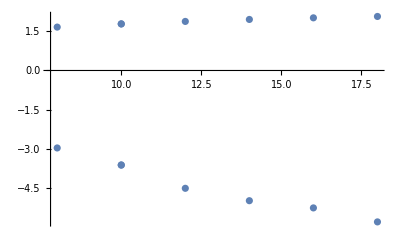

```mathematica
Map[{#n,1/(32π)#vector[α[0,0,0]]}&,Select[dataset,#variation==""&]]//ListPlot
```

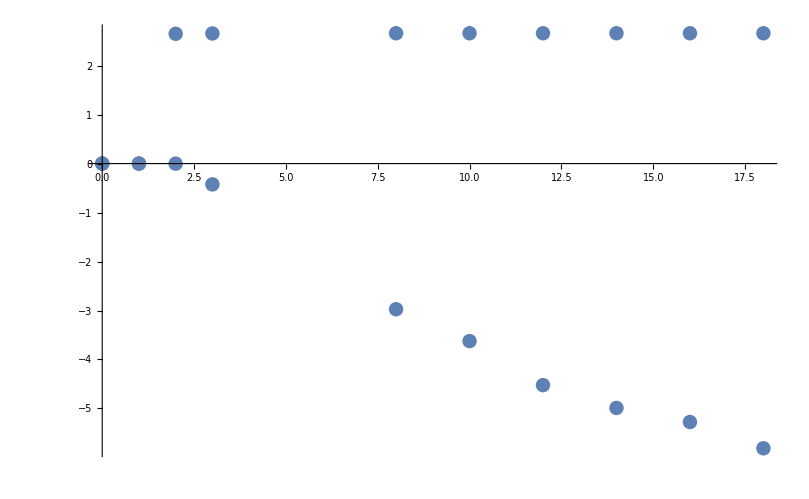

```mathematica
Map[{#n,1/(32π)#vector[α[0,0,0]]}&,Select[dataset,#variation=="imp_"&]]//ListPlot
```

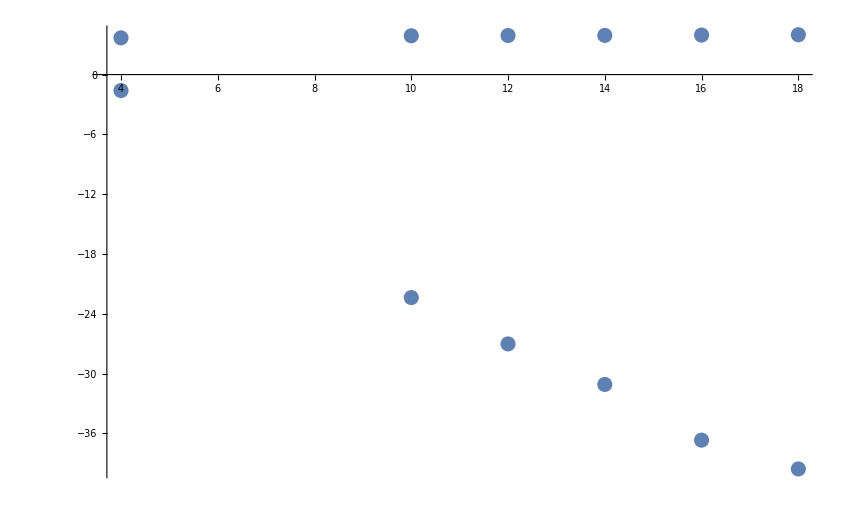

```mathematica
Map[{#n,1/(32π)#vector[α[0,0,0]]}&,Select[dataset,#variation=="with_pole_"&]]//ListPlot
```